# Harmonický ustálený stav (HUS), přenos, časová oblast, stejnosměrný stav

-Graphics-
Vstupní napětí  uZ[t]má sinusový průběh o frekvenci f=100 Hz.Fázor vstupního napětí má hodnotu Û=3+6j. Hodnoty součástek jsou následující:
R1=10 kΩ,
R2=10 kΩ,
R3=10 kΩ,
C2=10 nF,
L1=10 mH.
Překreslete obvod do stejnosměrného stavu a řešte pokud napětí uZ = 50mV.

### PODROBNÉ řešení příkladu ve stejnosměrném stavu

Nejprve je nutné z obvodu v zadání odstranit střídavý zdroj uZ[t] a nahradit jej zdrojem stejnosměrným uZ, dále pak z obvodu odstraníme kondenzátor C2 a cívku L nahradíme vodičem. Situaci popisuje obrázek níže:
-Graphics-
Tím, že jsme cívku L nahradili vodičem, došlo ke zkratování rezistoru R1 a můžeme jej z obvodu také vyřadit, tuto situaci popisuje následující obrázek:

-Graphics-
POZNÁMKA:
Proud jde vždy cestou nejmenšího odporu, pokud bychom rezistor R1 v obvodu nechali, proud by skrze něj neprocházel (což ale neumíme popsat rovnicemi 😜 proto jej z obvodu vyřadíme úplně a řešení tak lépe odpovídá skutečnosti).

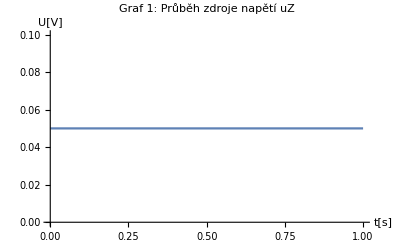

Výstupní napětí uout je uout = 0.05 V.

VYSVĚTLENÍ: K řešení tohoto typu úlohy ani žádné rovnice nepotřebujeme. Vidíme, že R2 není v obvodu zapojený a pokud jsme jako zde v ideálním světě můžeme jeho odpor při měření na svorkách zcela zanedbat. Rezistor R3 do obvodu sice zapojený je, ale protože je paralelně se zdrojem Uz visí na něm také stejné napětí jako na zdroji. Výsledné napětí tedy bude shodné se zdrojem Uz.

```mathematica
ClearAll["Global`*"]

(* Definice zdroje napětí *)
uZ = 50*10^-3;
tmax = 1;

Plot[uZ,{t,0,tmax}, AxesLabel->{"t[s]","U[V]"}, PlotLabel->"Graf 1: Průběh zdroje napětí uZ"] 

soucastky={
R2->10*10^3,
R3->10*10^3
};

uout = uZ;
Print["Výstupní napětí uout je uout = ",uout//N, " V."]

Print[ "VYSVĚTLENÍ: K řešení tohoto typu úlohy ani žádné rovnice nepotřebujeme. Vidíme, že R2 není v obvodu zapojený a pokud jsme jako zde v ideálním světě můžeme jeho odpor při měření na svorkách zcela zanedbat. Rezistor R3 do obvodu sice zapojený je, ale protože je paralelně se zdrojem Uz visí na něm také stejné napětí jako na zdroji. Výsledné napětí tedy bude shodné se zdrojem Uz."]
```